### Dynamical Systems TIF155/FIM770 Konstantinos Zakkas Problem set 2

### 2.3 Hopf bifurcation c)

```mathematica
f1[x_,y_] = -x^3;
g1[x_,y_] = 2y^3;
f2[x_,y_] = -x^2;
g2[x_,y_] = 2x^2;
```

```mathematica
ω1 = 3;
ω2 = -1;
```

```mathematica
For system (1)
```

```mathematica
fxxx=D[f1[x,y],{x,3}]
```

-6

```mathematica
fxyy= D[f1[x,y],{x,1},{y,2}]
```

0

```mathematica
gxxy = D[g1[x,y],{x,2},{y,1}]
```

0

```mathematica
gyyy = D[g1[x,y],{y,3}]
```

12

```mathematica
fxy = D[D[f1[x,y],{x}],{y}]
```

0

```mathematica
fxx = D[f1[x,y],{x,2}]
```

-6 x

```mathematica
fyy = D[f1[x,y],{y,2}]
```

0

```mathematica
gxy = D[D[g1[x,y],{x}],{y}]
```

0

```mathematica
gxx = D[g1[x,y],{x,2}]
```

0

```mathematica
gyy = D[g1[x,y],{y,2}]
```

12 y

```mathematica
α1 = fxxx+fxyy+gxxy+gyyy+1/ω1(fxy(fxx+fyy)-gxy(gxx+gyy)-fxx*gxx+fyy*gyy)-16α
```

6-16 α

```mathematica
Solve[α1==0]
```

{{α→3/8}}

```mathematica
α>0 so the bifurcation is subcritical
```

```mathematica
For system (2)
```

```mathematica
fxxx=D[f2[x,y],{x,3}]
```

0

```mathematica
fxyy= D[f2[x,y],{x},{y,3}]
```

0

```mathematica
gxxy = D[g2[x,y],{x,2},{y}]
```

0

```mathematica
gyyy = D[g2[x,y],{y,3}]
```

0

```mathematica
fxy = D[f2[x,y],{x},{y}]
```

0

```mathematica
fxx = D[f2[x,y],{x,2}]
```

-2

```mathematica
fyy = D[f2[x,y],{y,2}]
```

0

```mathematica
gxy = D[g2[x,y],{x},{y}]
```

0

```mathematica
gxx = D[g2[x,y],{x,2}]
```

4

```mathematica
gyy = D[g2[x,y],{y,2}]
```

0

```mathematica
α2 = fxxx+fxyy+gxxy+gyyy+1/ω2(fxy(fxx+fyy)-gxy(gxx+gyy)-fxx*gxx+fyy*gyy)-16α
```

-8-16 α

```mathematica
Solve[α2==0]
```

```mathematica
{{α->-1/2}}
α<0 so the bifurcations is supercritical
```

### d)

```mathematica
(*System 1*)
```

```mathematica
xDot[x_,y_,μ_] := μ x - 3y -x^3;
yDot[x_,y_,μ_] := 3x + μ y + 2y^3;
```

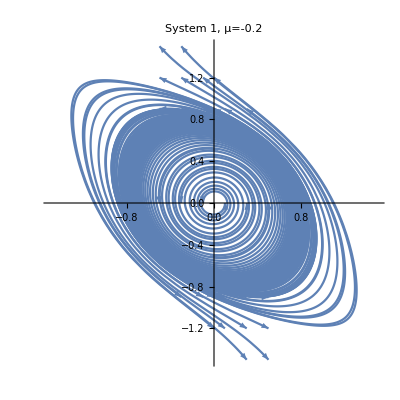

```mathematica
μ = -0.2;
t0 = 0;
tMax = -10;

sol= Table[NDSolve[{x'[t]==xDot[x[t],y[t],μ],
y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,t0,tMax}],{x0,{-0.5,-0.3, -0.1,0, 0.1, 0.3, 0.5}},{y0,{-1.5,-1.2, -0.9,0, 0.9, 1.2, 1.5}}];
Length[sol]
p1=ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tMax}, PlotRange->{{-1.5,1.5},{-1.5,1.5}}, PlotLabel->StringForm["System 1, μ=``",μ]]/.Line[x_]:>{Arrowheads[{0.05}],Arrow[x]}
```

```mathematica
μ = 0.2;
t0 = 0;
tMax = 7.7;

sol= Table[NDSolve[{x'[t]==xDot[x[t],y[t],μ],
y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,t0,tMax}],{x0,{-0.12,-0.08,-0.04,0.04,0.08,0.12}},{y0,{-0.12,-0.08,-0.04,0.04,0.08,0.12}}];

p2=ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tMax}, PlotRange->{{-1,1},{-1,1}},PlotLabel->StringForm["System 1, μ=``",μ]]/.Line[x_]:>{Arrowheads[{0.05}],Arrow[x]}
```

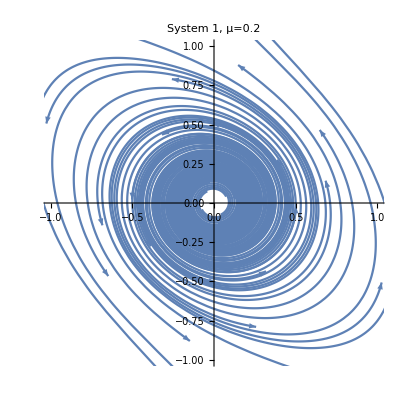

```mathematica
(*System 2*)
μ=.
xDot[x_,y_,μ_] := μ x +y -x^2;
yDot[x_,y_,μ_] := -x + μ y + 2x^2;
```

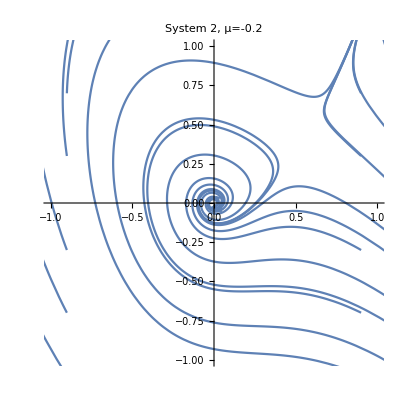

```mathematica
μ = -0.2;
t0 = 0;
tMax = 15;

sol= Table[NDSolve[{x'[t]==xDot[x[t],y[t],μ],
y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,t0,tMax}],{x0,{-1.5,-1.2,-0.9,0.9,1.2,1.5}},{y0,{-1.1,-0.7,-0.3,0.3,0.7,1.1}}];
p3=ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tMax}, PlotRange->{{-1,1},{-1,1}},PlotLabel->StringForm["System 2, μ=``",μ]]/.Line[x_]:>{Arrowheads[{{0.05},{0.05,0.5},{0.05}}],Arrow[x]}
```

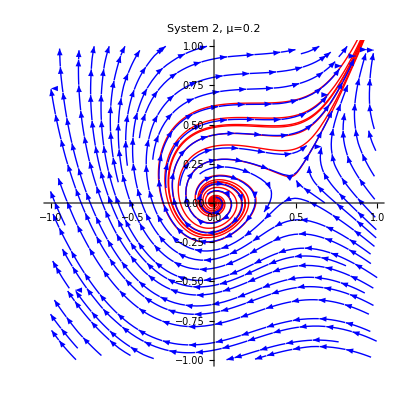

```mathematica
μ = 0.2;
t0 = -15;
tMax = 15;

sol= Table[NDSolve[{x'[t]==xDot[x[t],y[t],μ],
y'[t]==yDot[x[t],y[t],μ], x[0]==x0,y[0]==y0},{x[t],y[t]},{t,t0,tMax}],{x0,{-0.9,-0.5,-0.1, 0.1, 0.5,0.9}},{y0,{-0.9,-0.5,-0.1, 0.1, 0.5,0.9}}];
p4=ParametricPlot[{x[t],y[t]}/.sol,{t,t0,tMax}, PlotRange->{{-1,1},{-1,1}},
PlotStyle->{Red, Thick}, PlotLabel->StringForm["System 2, μ=``",μ]]/.Line[x_]:>{Arrowheads[{{0.05}}],Arrow[x]};
stream4 = StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-1,1},{y,-1,1}, StreamStyle->Blue, StreamColorFunction->None];
Show[{p4,stream4}]
```